## Lesson

Generate a middle C note:

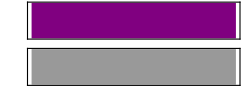

```mathematica
Sound[SoundNote["C"]]
```

Create a sound from notes:

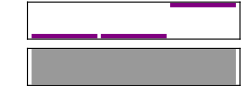

```mathematica
Sound[{SoundNote["C"],SoundNote["C"],SoundNote["G"]}]
```

Create a sound note with a pitch, duration and instrument:

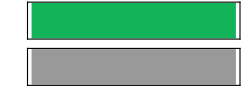

```mathematica
Sound[SoundNote[5,0.1,"Guitar"]]
```

## Questions

Q1. Generate the sequence of notes with pitches 0, 4 and 7.

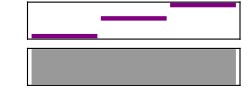

```mathematica
Sound[{SoundNote[0],SoundNote[4],SoundNote[7]}]
```

Q2. Generate 2 seconds of playing middle A on a cello.

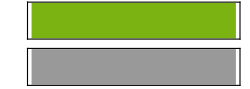

```mathematica
Sound[SoundNote["A",2,"Cello"]]
```

Q3. Generate a “riff” of notes from pitch 0 to pitch 48 in steps of 1, with each note lasting 0.05 seconds.

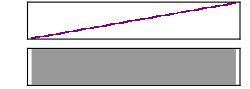

```mathematica
Sound[Table[SoundNote[i,0.06],{i,0,48,1}]]
```

Q4. Generate a sequence of notes going from pitch 12 down to 0 in steps of 1.

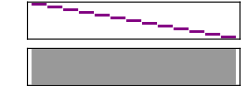

```mathematica
Sound[Table[SoundNote[i,0.2],{i,12,0,-1}]]
```

Q5. Generate a sequence of 5 notes starting with middle C, then successively going up by an octave at a time.

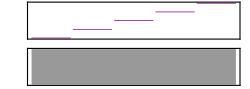

```mathematica
Sound[Table[SoundNote[12n],{n,0,4}]]
```

Q6. Generate a sequence of 10 notes on a trumpet with random pitches from 0 to 12 and duration 0.2 seconds.

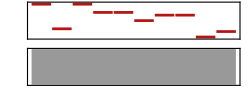

```mathematica
Sound[Table[SoundNote[RandomInteger[12],0.2,"Trumpet"],10]]
```

Q7. Generate a sequence of 10 notes with random pitches up to 12 and random durations up to 10 tenths of a second.

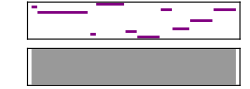

```mathematica
Sound[Table[SoundNote[RandomInteger[12],RandomInteger[10]/10],10]]
```

Q8. Generate 0.1-second notes with pitches given by the digits of 2^31.

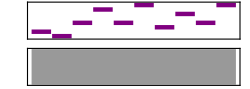

```mathematica
Sound[SoundNote[#,0.1]&/@IntegerDigits[2^31]]
```

Q9. Create a sound from the letters in CABBAGE, each playing for 0.3 seconds sounding like a guitar.

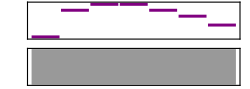

```mathematica
Sound[SoundNote[#,0.1]&/@Characters["CABBAGE"]]
```

Q10. Generate 0.1-second notes with pitches given by the letter numbers of the characters in “wolfram”.

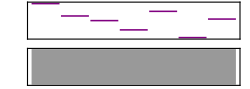

```mathematica
Sound[SoundNote[LetterNumber[#],0.1]&/@Characters["wolfram"]]
```

## Extended Questions

+Q1. Generate a sequence of three notes of 1 second of playing middle D on the cello, piano and guitar.

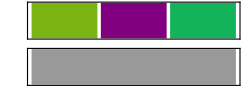

```mathematica
Sound[SoundNote["D",1,#]&/@{"Cello","Piano","Guitar"}]
```

+Q2. Generate a sequence of notes from pitch 0 to pitch 12, going up in steps of 3.

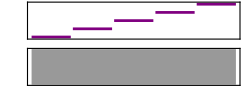

```mathematica
Sound[SoundNote[#,1]&/@Range[0,12,3]]
```

+Q3. Generate a sequence of 5 notes starting with middle C, then successively going up by a perfect fifth (7 semitones) at a time.

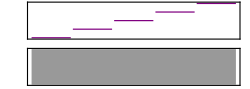

```mathematica
Sound[SoundNote[7#,1]&/@Range[0,4]]
```

+Q4. Generate 0.02-second notes with pitches given by the lengths of the names of integers from 1 to 200.

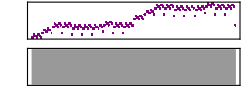

```mathematica
Sound[SoundNote[#,0.02]&/@StringLength[IntegerName[Range[200]]]]
```